Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

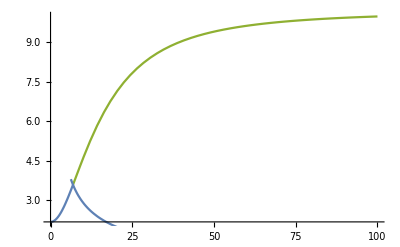

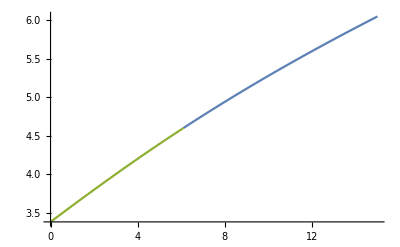

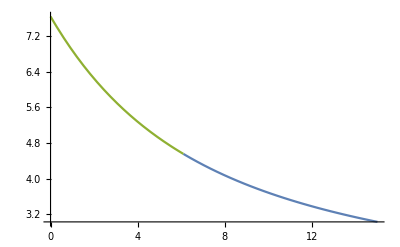

```mathematica
parameters = {
Ω->5,
α1->6,
k1 -> 5, K1 -> Ω*3,
k2 -> 5, K2 ->Ω* 3,
k3->10.0, K3->Ω*2};
eqs={
Ω*α + ((Ω*k1)/((K1/x2)^2+1)) x1-((Ω*k3)/((K3/x1)^2+1))*x1,
Ω*α1+ ((Ω*k2)/((K2/x1)^2+1))x2 -((Ω*k3)/((K3/x1)^2+1))*x2
} //. parameters;
soln = Solve[eqs==0,{x1,x2}, Reals, Assumptions->{x1>=0, x2>=0}] ;
s1 = Solve[Part[eqs,1]==0, x1, Reals, Assumptions->{x1>=0, x2>=0}]//. α->1.0;
s2 = Solve[Part[eqs,2]==0,x1, Reals, Assumptions->{x1>=0,x2>=0}]//. α->1.0;
p1 = Plot[Evaluate[x1/.s1],{x2,0,100}];
p2 = Plot[Evaluate[x1/.s2],{x2,0,100}];
Show[p1,p2]
p1 = Plot[Evaluate[x1/.soln], {α,0, 15.0}];
p2 = Plot[Evaluate[x2/.soln], {α,0, 15.0}];
Show[p1]
Show[p2]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

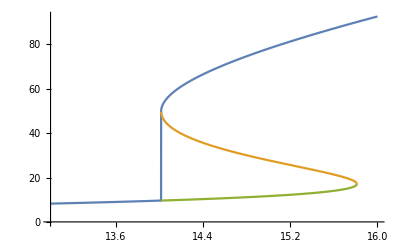

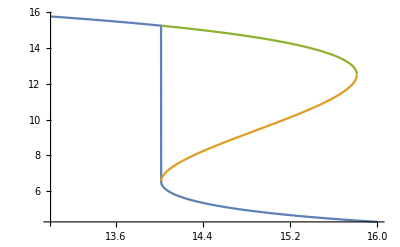

```mathematica
parameters = {
Ω-> 3,
γ->0.1,
α-> Ω*0.1,
		          K1 ->Ω*5,
k2 ->Ω*5,      K2 ->Ω*5,
k3->Ω*1.0,  K3->Ω*10};
eqs={
 (k/((x2/K1)^2+1)) -(k3/((K3/x2)^2+1)+γ)x1,
  α + (k2/((x1/K2)^2+1))  -(k3/((K3/x2)^2+1)+γ)x2 }//. parameters;
soln = Solve[eqs==0,{x1,x2}, Reals] ;
p1 = Plot[Evaluate[x1/.soln], {k,13, 16.0}];
p2 = Plot[Evaluate[x2/.soln], {k,13, 16.0}];
Show[p1]
Show[p2]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

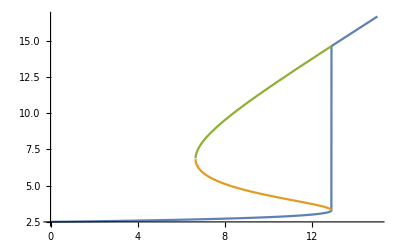

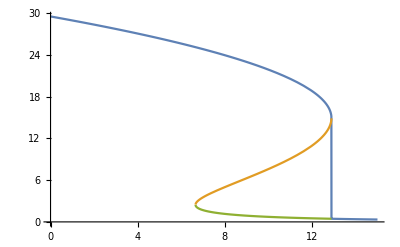

```mathematica
parameters = {
		  K1 ->3,
k2 -> 10, K2 ->3,
k3->1.0,K3->5.0};
eqs={
0.5+ (k/((x2/K1)^2+1)) -(k3/((K3/x1)^2+1))x1,
(k2/((x1/K2)^2+1))-(k3/((K3/x1)^2+1))x2} //. parameters;
soln = Solve[eqs==0,{x1,x2}, Reals] ;
p1 = Plot[Evaluate[x1/.soln], {k,0, 15.0}];
p2 = Plot[Evaluate[x2/.soln], {k,0, 15.0}];
Show[p1]
Show[p2]
```